# Debye shielding

## Debye length

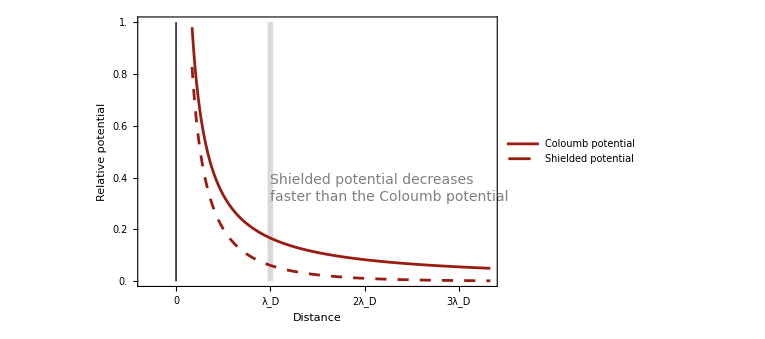

```mathematica
c=5;
λD=30;
ϕC[r_]:=c(1/r);
ϕD[r_]:=c(1/r)Exp[-r/λD];

gfDebye=Plot[

{ϕC[r],ϕD[r]},{r,c*1.02,100},

Prolog->{
{LightGray,AbsoluteThickness[4],Line[{{λD,0},{λD,1}}]}
},

Epilog->{
{Black,AbsoluteThickness[1],Line[{{0,0},{0,1}}]},
Text[Style["Shielded potential decreases \nfaster than the Coloumb potential",FontColor->Gray,FontSize->14,FontWeight->Plain,TextAlignment->Left],{λD,.3},{-1.1,-1}]
},

PlotRange->{{-10,100},{0,1}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

PlotStyle->{
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2]},
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2],AbsoluteDashing[8]}
},

PlotLegends->Placed[
LineLegend[
{"Coloumb potential","Shielded potential"},
LegendMarkerSize->{{30,10}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->"Column"],
{Scaled@({.95,.9}),{1,1}}],

Axes->False,
Frame->True,
FrameTicks->{
{Table[{i,i,{.015,0}},{i,0,1,.2}],
Table[{i,Null,{.015,0}},{i,0,1,.2}]},
{Union[{{0,0,{.015,0}},{λD,StringForm["`1`",Subscript["λ","D"]],{.015,0}}},Table[{λD i,StringForm["`1``2`",i,Subscript["λ","D"]],{.015,.0}},{i,2,Floor[100/λD]}]],
Table[{λD i,Null,{.015,.0}},{i,0,Floor[100/λD]}]}
},
FrameLabel->{{"Relative potential",None},{"Distance",None}},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

GridLines->None,

ImagePadding->{{50,10},{45,10}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->0.6

];

Print[gfDebye];
```

## Cartoon

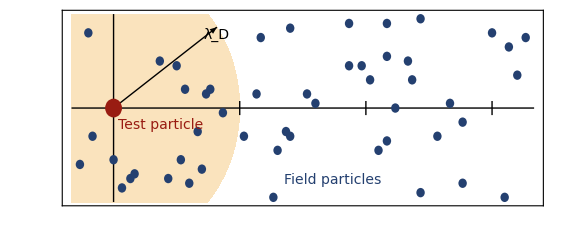

```mathematica
(* -- test particle -- *)
qT={
EdgeForm[Transparent],
FaceForm[{RGBColor[.60,.11,.07,1]}],
Disk[{0,0},2]
};

(* -- field particle -- *)
xRange={x1,x2}={-10,100};
yRange={y1,y2}={-20,20};
(*ptsRandom=Table[{RandomInteger[xRange-{-1,1}],RandomInteger[yRange-{-1,1}]},50];*)
(*ptsSel=Select[ptsRandom,(√(Total@(#^2))>3)&];*)
ptsSel={{67,0},{80,1},{16,-11},{2,-17},{56,18},{5,-14},{13,-15},{17,4},{41,-5},{71,6},{23,4},{26,-1},{15,9},{83,-16},{42,17},{94,13},{39,-9},{73,-18},{18,-16},{63,-9},{77,-6},{34,3},{-8,-12},{22,3},{65,18},{61,6},{56,9},{65,-7},{38,-19},{70,10},{90,16},{20,-5},{46,3},{-6,16},{35,15},{59,9},{83,-3},{48,1},{-5,-6},{96,7},{0,-11},{4,-15},{11,10},{21,-13},{93,-19},{73,19},{98,15},{65,11},{42,-6},{31,-6}};
qF={
EdgeForm[Transparent],
FaceForm[{RGBColor[.14,.25,.44,1]}],
Disk[#,1]
}&/@ptsSel;

(*Show[Graphics[{qT,qF}]];*)

(* -- plot -- *)
gfCharge=RegionPlot[

x^2+y^2<λD^2
&&Between[y,yRange]
&&x≥x1,
{x,x1,x2},{y,y1,y2},

PlotRange->{xRange,yRange},
PlotRangePadding->0,
PlotRangeClipping->False,

PlotPoints->100,

Epilog->{
{Black,AbsoluteThickness[1],Arrowheads[{0,.03}],Arrow[{{0,0},λD{Cos[35°],Sin[35°]}}]},
Text[Style[StringForm["`1`",Subscript["λ","D"]],FontColor->Black,FontSize->14,FontWeight->Plain],λD{Cos[35°],Sin[35°]},{0,2}],
{Black,AbsoluteThickness[1],Line[{{x1,0},{x2,0}}]},
{Black,AbsoluteThickness[1],Line[{{0,y1},{0,y2}}]},
Table[{Black,AbsoluteThickness[1],Line[{{i λD,-1.5},{i λD,1.5}}]},{i,3}],
qF,qT,
Text[Style["Test particle",FontColor->RGBColor[.60,.11,.07,1],FontSize->14,FontWeight->Plain],{1,-2},{-1,1}],
Text[Style["Field particles",FontColor->RGBColor[.14,.25,.44,1],FontSize->14,FontWeight->Plain],{52,-15},{0,0}]
},

BoundaryStyle->None,
PlotStyle->Directive[RGBColor[.98,.89,.74,1]],

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

Axes->True,
AxesOrigin->{0,0},
AxesStyle->Directive[Black,AbsoluteThickness[1]],

Frame->True,
FrameTicks->None,
FrameStyle->Directive[Black,AbsoluteThickness[1]],

GridLines->None,

ImagePadding->{{50,10},{5,5}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->Automatic


];

Print[gfCharge];
```

## Merge figures

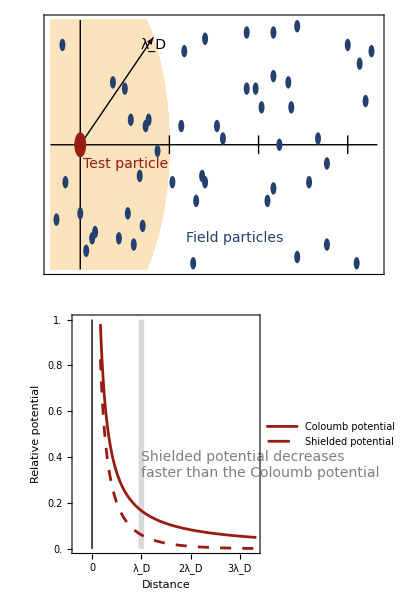

```mathematica
gf=Grid[{{gfCharge},{gfDebye}}];
Print[gf];

Export[NotebookDirectory[]<>"shielding.pdf",gf];
```

# Debye number

## Classical analysis

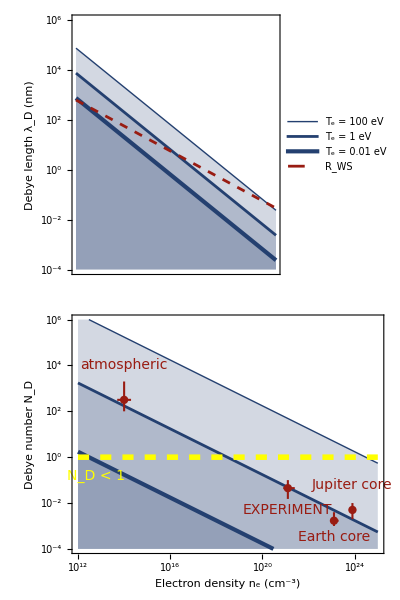

```mathematica
(* -- functions -- *)
Clear[λDFunc,nDFunc,wsFunc,λD,nD,ne,Te];
λDFunc[ne_:10^21(*[cm^-3]*),Te_:1(*[eV]*)]:=Block[{ϵ0,e,λD},
ϵ0=8.854*^-12;
e=1.6*^-19;
λD=√((ϵ0 Te)/((ne*10^6) e));
Return[λD]
];
wsFunc[ne_: 10^21(*[cm^-3]*)]:=((4π)/3(ne*10^6))^(-1/3);
nDFunc[ne_:10^21(*[cm^-3]*),Te_:1(*[eV]*)]:=(4π)/3 λDFunc[ne,Te]^3 (ne*10^6);

(* -- discrete data -- *)
dta={Table[{x,9+Log10@λDFunc[10^x,100]},{x,12,25,1}],
Table[{x,9+Log10@λDFunc[10^x,1]},{x,12,25,1}],
Table[{x,9+Log10@λDFunc[10^x,.01]},{x,12,25,1}],
Table[{x,9+Log10@wsFunc[10^x]},{x,12,25,1}]};
dtb={Table[{x,Log10@nDFunc[10^x,100]},{x,12,25,1}],
Table[{x,Log10@nDFunc[10^x,1]},{x,12,25,1}],
Table[{x,Log10@nDFunc[10^x,.01]},{x,12,25,1}]
};

(* -- plot -- *)
clr=RGBColor[.60,.11,.07,1];
gfa=ListLinePlot[

dta,

Epilog->{
Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]
},

Joined->True,
PlotRange->{{12,25},{-4,6}},
PlotRangePadding->0,

PlotStyle->{
{RGBColor[.14,.25,.44,1],AbsoluteThickness[1]},
{RGBColor[.14,.25,.44,1],AbsoluteThickness[2]},
{RGBColor[.14,.25,.44,1],AbsoluteThickness[3]},
{clr,AbsoluteThickness[2],AbsoluteDashing[6]}
},

PlotLegends->Placed[LineLegend[
{StringForm["`1` = 100 eV",Subscript[Style["T",Italic],"e"]],
StringForm["`1` = 1 eV",Subscript[Style["T",Italic],"e"]],
StringForm["`1` = 0.01 eV",Subscript[Style["T",Italic],"e"]],
"R_WS"},
LegendLayout->"Column"],{{.97,.92},{1,1}}],

Axes->False,
Frame->True,
FrameLabel->{{StringForm["Debye length `1` (nm)",Subscript["λ","D"]],None},{None,None}},
FrameTicks->{
{Table[{i,If[Mod[i,2]==0,Superscript[10,i],Null],{If[Mod[i,2]==0,.015,.008],0}},{i,-4,6}],Table[{i,Null,{If[Mod[i,2]==0,.015,.008],0}},{i,-4,6}]},
{Table[{i,Null,{If[Mod[i,2]==0,.015,.008],0}},{i,12,25}],
Table[{i,Null,{If[Mod[i,2]==0,.015,.008],0}},{i,12,25}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,

PlotRangeClipping->False,
ImagePadding->{{55,5},{45,15}},
ImageSize->(130*2)*(72/25.4),
AspectRatio->.4,

Filling->{{1->Bottom},{2->Bottom},{3->Bottom}}

];

gfb=ListLinePlot[

dtb,

Epilog->{
(* panel label *)
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
(* Subscript[N, D] < 1 *)
{Yellow,AbsoluteThickness[4],AbsoluteDashing[8],Line[{{12,0},{25,0}}]},
Text[Style["N_D < 1",FontSize->14,FontWeight->Plain,FontColor->Yellow],{12.8,-.8},{0,0}],
(* atmospheric conditions *)
{clr,AbsoluteThickness[1.5],Line[{{13.7,2.5},{14,2.5},{14.3,2.5}}],Line[{{14,2},{14,2.5},{14,3.3}}]},
{clr,AbsolutePointSize[6],Point[{14,2.5}]},
Text[Style["atmospheric",FontSize->14,FontWeight->Plain,FontColor->clr],{14,4},{0,0}],
(* high pressure conditions *)
{clr,AbsoluteThickness[1.5],Line[{{20.9,-1.35},{21.1,-1.35},{21.4,-1.35}}],Line[{{21.1,-1.82},{21.1,-1.35},{21.1,-1}}]},
{clr,AbsolutePointSize[6],Point[{21.1,-1.35}]},
Text[Style["EXPERIMENT",FontSize->14,FontWeight->Plain,FontColor->clr],{21.1,-2.3},{0,0}],
(* Earth core conditions *)
{clr,AbsoluteThickness[1.5],Line[{{23.0,-2.77},{23.1,-2.77},{23.3,-2.77}}],Line[{{23.1,-3},{23.1,-2.77},{23.1,-2.4}}]},
{clr,AbsolutePointSize[6],Point[{23.1,-2.77}]},
Text[Style["Earth core",FontSize->14,FontWeight->Plain,FontColor->clr],{23.1,-3.5},{0,0}],
(* Jupiter core conditions *)
{clr,AbsoluteThickness[1.5],Line[{{23.8,-2.3},{23.9,-2.3},{24.0,-2.3}}],Line[{{23.9,-2.7},{23.9,-2.3},{23.9,-2}}]},
{clr,AbsolutePointSize[6],Point[{23.9,-2.3}]},
Text[Style["Jupiter core",FontSize->14,FontWeight->Plain,FontColor->clr],{23.9,-1.5},{0,-1}]
},

Joined->True,
PlotRange->{{12,25},{-4,6}},
PlotRangePadding->0,

PlotStyle->{
{RGBColor[.14,.25,.44,1],AbsoluteThickness[1]},
{RGBColor[.14,.25,.44,1],AbsoluteThickness[2]},
{RGBColor[.14,.25,.44,1],AbsoluteThickness[3]}
},

Axes->False,
Frame->True,
FrameLabel->{{StringForm["Debye number `1`",Subscript["N","D"]],None},{StringForm["Electron density `1` (cm^-3)",Subscript[Style["n",Italic],"e"]],None}},
FrameTicks->{
{Table[{i,If[Mod[i,2]==0,Superscript[10,i],Null],{If[Mod[i,2]==0,.015,.008],0}},{i,-4,6}],Table[{i,Null,{If[Mod[i,2]==0,.015,.008],0}},{i,-4,6}]},
{Table[{i,If[Mod[i,2]==0,Superscript[10,i],Null],{If[Mod[i,2]==0,.015,.008],0}},{i,12,25}],
Table[{i,Null,{If[Mod[i,2]==0,.015,.008],0}},{i,12,25}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,

PlotRangeClipping->False,
ImagePadding->{{55,5},{45,15}},
ImageSize->(130*2)*(72/25.4),
AspectRatio->.4,

Filling->{{1->Bottom},{2->Bottom},{3->Bottom},{4->Bottom}}

];

gf=Grid[{{gfa},{gfb}}];
Print[gf];

Export[NotebookDirectory[]<>"number.pdf",gf];
```